最小二乗法、行列計算、フックの法則

```mathematica
xi= {5,10,15,20,25,30,35,40,45,50}(*重さ*)
```

{5,10,15,20,25,30,35,40,45,50}

```mathematica
yi={5.4,5.7, 6.9, 6.4, 8.2, 7.7, 8.4, 10.1,9.9,10.5}(*伸び*)
```

{5.4,5.7,6.9,6.4,8.2,7.7,8.4,10.1,9.9,10.5}

```mathematica
data=Transpose[{xi,yi}];
data//MatrixForm
```

(5 | 5.4
10 | 5.7
15 | 6.9
20 | 6.4
25 | 8.2
30 | 7.7
35 | 8.4
40 | 10.1
45 | 9.9
50 | 10.5)

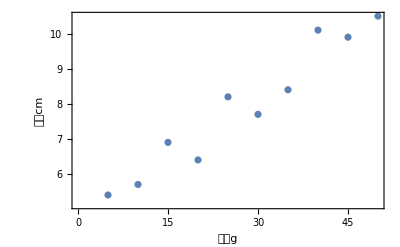

```mathematica
p1=ListPlot[data,Frame->True,FrameLabel->{重さg,伸びcm},FrameStyle->20]
```

```mathematica
εi=yi-β1 xi-β0;
```

```mathematica
εi//MatrixForm
```

(5.4-β0-5 β1
5.7-β0-10 β1
6.9-β0-15 β1
6.4-β0-20 β1
8.2-β0-25 β1
7.7-β0-30 β1
8.4-β0-35 β1
10.1-β0-40 β1
9.9-β0-45 β1
10.5-β0-50 β1)

```mathematica
s=εi.εi
```

(10.5-β0-50 β1)^2+(9.9-β0-45 β1)^2+(10.1-β0-40 β1)^2+(8.4-β0-35 β1)^2+(7.7-β0-30 β1)^2+(8.2-β0-25 β1)^2+(6.4-β0-20 β1)^2+(6.9-β0-15 β1)^2+(5.7-β0-10 β1)^2+(5.4-β0-5 β1)^2

```mathematica
eq1=D[s, β0]==0
```

-2 (10.5-β0-50 β1)-2 (9.9-β0-45 β1)-2 (10.1-β0-40 β1)-2 (8.4-β0-35 β1)-2 (7.7-β0-30 β1)-2 (8.2-β0-25 β1)-2 (6.4-β0-20 β1)-2 (6.9-β0-15 β1)-2 (5.7-β0-10 β1)-2 (5.4-β0-5 β1)==0

```mathematica
eq2=D[s, β1]==0
```

-100 (10.5-β0-50 β1)-90 (9.9-β0-45 β1)-80 (10.1-β0-40 β1)-70 (8.4-β0-35 β1)-60 (7.7-β0-30 β1)-50 (8.2-β0-25 β1)-40 (6.4-β0-20 β1)-30 (6.9-β0-15 β1)-20 (5.7-β0-10 β1)-10 (5.4-β0-5 β1)==0

```mathematica
連立方程式の解=Solve[{eq1,eq2},{β0,β1}]
```

{{β0→4.69333,β1→0.117333}}

```mathematica
線形回帰式=β0+β1 x/.連立方程式の解
```

{4.69333+0.117333 x}

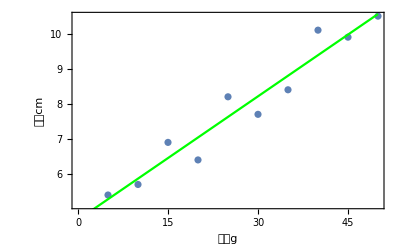

```mathematica
Show[p1,Plot[線形回帰式,{x,0,50},PlotStyle->Green]]
```

```mathematica
FindFit[data,β0+β1 x,{β0,β1},x]
```

{β0→4.69333,β1→0.117333}